#### Initial Work on Newton relaxation. I am thinking that NMinimize with constraints may be a better method to find a better solution

```mathematica
findNotNearestNeighborUpToDistance[positions_,nf_,whichParticle_,beyondNearstNeighbor_, distance_]:=Block[{nnn},
nnn=Select[Abs[#Index-whichParticle] >1 &][nf[positions[[whichParticle]],{beyondNearstNeighbor + 3,distance}]];
Which[
nnn!={},Join[<|"Me"-> whichParticle|>,#]&/@nnn,
True,{}
]
]
```

```mathematica
checkCollisions[positions_,nf_,whichParticle_,beyondNearstNeighbor_,distance_]:= Block[{numberCollisions},
numberCollisions=Echo@Length[findNotNearestNeighborUpToDistance[positions,nf,whichParticle,beyondNearstNeighbor,distance]];
If[
numberCollisions > 0,Throw[numberCollisions]
];
numberCollisions
]
```

#### The following has not be checked. So far, only the newton relaxation has been check.

```mathematica
displacementsNew[perturbedIndex_,positionList_,s_,ν_,θ_,OptionsPattern[]]:= 
Block[{displacement,displacedPositions,betaList,Δ , computedPositions,collisionDistance,results,overlap,minDistances ,currentNearest,indexRules, selectCollisions},
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
displacement[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
computedPositions = {displacement[perturbedIndex]};
indexRules=<|1->perturbedIndex|>;
selectCollisions=Select[Abs[#Particle - #OtherParticle]> 1 && #Distance <1&];
(*#1*)
 displacement[index_] := displacement[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex],myDisplacement},
myDisplacement=displacement[index-nextIndex ]+ Δ[[index]];
AppendTo[computedPositions,myDisplacement];
AssociateTo[indexRules,Length[computedPositions]->index];
myDisplacement
];

newPositions = displacement/@Range[Length[Δ]];
currentNearest =Nearest[newPositions->All];
If[
0== Catch[MapIndexed[checkCollisions[#1,currentNearest,#2[[1]],2,1]&,newPositions]],
Return[newPositions],
True,Return[newtonRelaxation[newPositions,currentNearest]]
]
]
```

Not sure if this is too singular, but it needs to go to zero at r=1

```mathematica
energy =With[{r = Sqrt[(xOther - xMe)^2 + (yOther - yMe)^2]},1/r^12]
```

1/(((-xMe+xOther)^2+(-yMe+yOther)^2)^6)

```mathematica
Grad[-energy,{xMe,yMe}]
```

{-(12 (-xMe+xOther))/(((-xMe+xOther)^2+(-yMe+yOther)^2)^7),-(12 (-yMe+yOther))/(((-xMe+xOther)^2+(-yMe+yOther)^2)^7)}

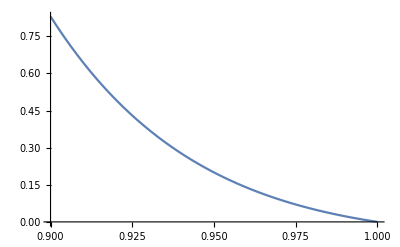

```mathematica
Plot[(1-x^2)/x^14,{x,.9,1}]
```

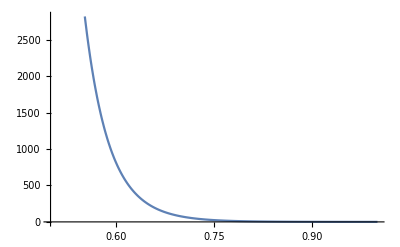

```mathematica
Plot[(1-x^2)/x^14,{x,0.5,1}]
```

```mathematica
force[pMe:{xMe_,yMe_},pOther:{xOther_,yOther_}]:= Block[{dp = pOther-pMe,magSq},
magSq= dp.dp;
(-dp (1-magSq))/(magSq)^4]
```

```mathematica
computeForceInNeighborhood[position_,neighborhood_List]:=
Block[{ positions},
If[Length[neighborhood]==0,Return[{0,0}]];
positions =neighborhood[[All,"Element"]];
Total[force[position,#]&/@positions]
]
```

```mathematica
newtonRelaxation[positions_,nf_]:= Block[{relaxedPositions = positions, forces,maxForceMagnitude,neighborhoods, currentNearest = nf,overlaps,selector =Select[#Distance < 1&],icount=0},
neighborhoods =Select[!PossibleZeroQ[#Distance]&][#]&/@currentNearest[relaxedPositions,{13,1}];
overlaps =Length[Flatten[selector/@neighborhoods]];
While[overlaps >0 && icount++ < 200,
forces =MapThread[computeForceInNeighborhood[#1,#2]&,{relaxedPositions,neighborhoods}];
maxForceMagnitude = Max[Norm/@forces];
If[maxForceMagnitude==0,Break[]];
forces = 0.01 forces/maxForceMagnitude; (*is 0.01 a good choice?*)
relaxedPositions += forces;
currentNearest=Nearest[relaxedPositions->All];
neighborhoods =Select[!PossibleZeroQ[#Distance]&][#]&/@currentNearest[relaxedPositions,{13,1}];
overlaps =Length[Flatten[Select[#Distance < 1&][#]&/@neighborhoods]];
];
{overlaps,relaxedPositions}
]
```

```mathematica
positions=AnglePath[ConstantArray[0.565,10]]
```

{{0.,0.},{0.844589,0.535416},{1.27125,1.43983},{1.14736,2.43212},{0.511441,3.20388},{-0.438861,3.51521},{-1.40817,3.26935},{-2.09519,2.54271},{-2.2864,1.56116},{-1.92235,0.629785},{-1.1162,0.038069}}

#### displacements is the non-collision detecting version in the beginning of Random_Motion_of_Polymer.nb

```mathematica
positions=displacements[11,positions,.126,.1,0]
```

{{-0.502952,0.0040433},{0.371188,0.489717},{0.885964,1.34704},{0.874841,2.34698},{0.311374,3.17312},{-0.626668,3.51964},{-1.58831,3.24533},{-2.2107,2.46263},{-2.29072,1.46583},{-1.83258,0.576948},{-0.990202,0.038069}}

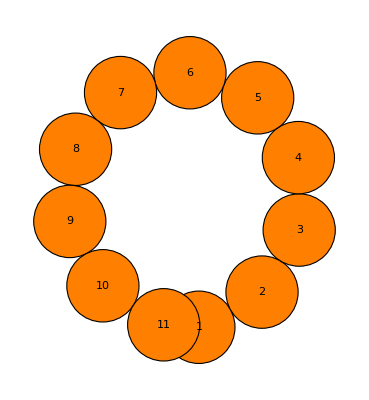

```mathematica
Graphics[chainGraphic[positions]]
```

```mathematica
Length[positions]
```

11

```mathematica
nf= Nearest[positions->All]
```

NearestFunction[…]

```mathematica
{overlaps,relaxedPositions}=newtonRelaxation[positions,nf]
```

{0,{{-0.244544,-0.177238},{0.480392,0.51215},{0.959119,1.39084},{0.899941,2.38963},{0.315799,3.20186},{-0.625326,3.54143},{-1.58988,3.27574},{-2.23359,2.50979},{-2.36414,1.51777},{-1.95471,0.60468},{-1.24183,-0.0972952}}}

```mathematica
Union[Flatten[DistanceMatrix[relaxedPositions]]]
```

{0.,1.00039,1.00047,1.00048,1.00048,1.00048,1.00051,1.00052,1.00054,1.00057,1.00063,1.00069,1.82687,1.88044,1.90711,1.9107,1.9113,1.92092,1.92189,1.92378,1.92541,1.96673,1.97678,2.43686,2.64165,2.6428,2.65682,2.66808,2.67124,2.69474,2.69586,2.71399,2.78935,2.81045,3.01706,3.01802,3.13583,3.16516,3.17021,3.22362,3.22477,3.28207,3.32568,3.34311,3.36676,3.3699,3.37852,3.38311,3.39095,3.42524,3.44971,3.45304,3.64837,3.69058,3.70581,3.73811}

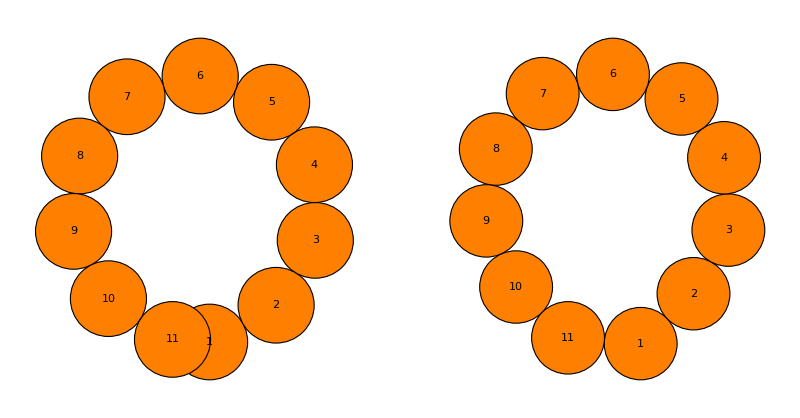

```mathematica
GraphicsRow[{Graphics[chainGraphic[positions]],Graphics[chainGraphic[relaxedPositions]]}]
```

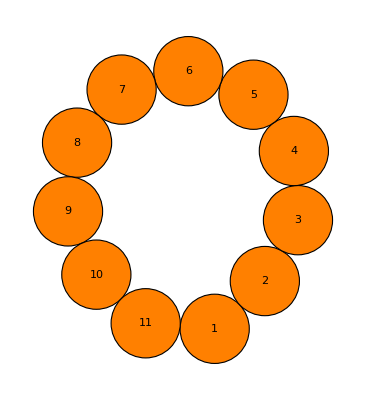

```mathematica
Graphics[chainGraphic[tmp]]
```

```mathematica
Plot[(1-x^2)/x^12,{x,0.5,1}]
```

-Graphics-

torque to change α:

```mathematica
Simplify[Cos[ArcSin[dgr Sin[ϕ - α]/dbg]], Assumptions->0 < dbg < 1 && dgr >1 && 0 < ϕ < 2Pi && 0 < α < 2Pi]
```

√(1-(dgr^2 Sin[α-ϕ]^2)/dbg^2)

```mathematica
Manipulate[
Graphics[
{
{Red,Circle[{0,0},1/2]},
{Blue,Circle[AngleVector[α],1/2]},
{Green,Circle[dgr AngleVector[ϕ],1/2]},
{FaceForm[], EdgeForm[Black],Polygon[{dgr AngleVector[ϕ],AngleVector[α],   {0,0}} ]},
{Line[1/2{ AngleVector[α], AngleVector[α] + 1 AngleVector[α-Pi/2]}],
Line[1/2{ AngleVector[α], AngleVector[α] + 1 AngleVector[α+Pi/2]}]
}
}
],
{α,0,2 π},
{ϕ,0,2 π},
{dgr,1/2,2},
{dbg,1,2}

]
```

## Using torques, idea is that the angle between particles relax and thus maintains next-neighbor distances.

```mathematica
energy =Module[{
pg =dgr AngleVector[ϕ],
pb =  AngleVector[α],
},
delta= pg-pb;
r = Sqrt[delta.delta];1/r^12]
```

1/(((-Cos[α]+dgr Cos[ϕ])^2+(-Sin[α]+dgr Sin[ϕ])^2)^6)

```mathematica
torque =FullSimplify[-D[energy,α], Assumptions->Assumptions->Δ>0 && 0 < ϕ < 2Pi && 0 < α < 2Pi]
```

(12 dgr Sin[α-ϕ])/((1+dgr^2-2 dgr Cos[α-ϕ])^7)

```mathematica
With[{torque= torque},
Manipulate[
Graphics[
{
{Red,Circle[{0,0},1/2]},
{Blue,Circle[AngleVector[α],1/2]},
{Green,Circle[dgr AngleVector[ϕ],1/2]},
{FaceForm[], EdgeForm[Black],Polygon[{dgr AngleVector[ϕ],AngleVector[α],   {0,0}} ]},
{Line[1/2{ AngleVector[α], AngleVector[α] + 2 AngleVector[α-Pi/2]}],
Line[1/2{ AngleVector[α], AngleVector[α] + 2 AngleVector[α+Pi/2]}]
}
}
],
{α,0,2 π},
{ϕ,0,2 π},
{dgr,1/2,2},
{dbg,1,2},
Dynamic[torque]

]
]
```

```mathematica
nf =Nearest[positions->All]
```

NearestFunction[…]

```mathematica
nnn=findNotNearestNeighborUpToDistance[positions,nf,#,12, 1]&/@Range[Length[positions]]
```

{{<|Me→1,Element→{-0.990202,0.038069},Index→11,Distance→0.488437|>},{},{},{},{},{},{},{},{},{},{<|Me→11,Element→{-0.502952,0.0040433},Index→1,Distance→0.488437|>}}

```mathematica
With[
{nnn=findNotNearestNeighborUpToDistance[positions,nf,#,12, 1]&/@Range[Length[positions]]},
Echo[nnn];
MapIndexed[If[AssociationQ[#1],AssociateTo[<|"Me"-> #2[[1]]|>,#1]]&,nnn]
]
```

{{<|Element→{-0.990202,0.038069},Index→11,Distance→0.488437|>},{},{},{},{},{},{},{},{},{},{<|Element→{-0.502952,0.0040433},Index→1,Distance→0.488437|>}}

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
nnn=findNotNearestNeighborUpToDistance[positions,nf,#,12, 1]&/@Range[Length[positions]]
```

{{<|Me→1,Element→{-0.990202,0.038069},Index→11,Distance→0.488437|>},{},{},{},{},{},{},{},{},{},{<|Me→11,Element→{-0.502952,0.0040433},Index→1,Distance→0.488437|>}}

```mathematica
Clear[torque]
```

```mathematica
computeTorque[dr_,α_]:= With[{dgr = Sqrt[dr.dr],ϕ = ArcTan@@dr},
(12 dgr Sin[α-ϕ])/((1+dgr^2-2 dgr Cos[α-ϕ])^7)
]
```

```mathematica
getTorques[positions_,neighborhoodOverlaps_,index_]:= Block[{torque=0,α,ϕ,dgr},
If[Flatten[neighborhoodOverlaps]=={}  || !( 1< index < Length[positions]),Return[0]];

If[
neighborhoodOverlaps[[index-1]]!={},
α =ArcTan@@(positions[[index-1]]- positions[[index]]);
torque+= Total[computeTorque[#Element- positions[[index]],α]&/@neighborhoodOverlaps[[index-1]]];
];
If[
neighborhoodOverlaps[[index+1]]!={},
α = ArcTan@@(positions[[index+1]]- positions[[index]]);
torque+= Total[computeTorque[#Element- positions[[index]],α]&/@neighborhoodOverlaps[[index+1]]];
];
torque
]
```

```mathematica
index = 2
```

2

```mathematica
torque = 0
```

0

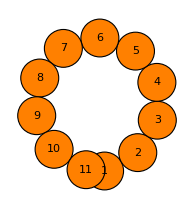

```mathematica
getTorques[positions,nnn,#]&/@Range[11]
```

{0,72674.5,0,0,0,0,0,0,0,-63812.9,0}

```mathematica
neighborhoodOverlaps=nnn
```

{{<|Me→1,Element→{-0.990202,0.038069},Index→11,Distance→0.488437|>},{},{},{},{},{},{},{},{},{},{<|Me→11,Element→{-0.502952,0.0040433},Index→1,Distance→0.488437|>}}

```mathematica
nnn[[index-1]]!={}
```

True

```mathematica
α = ArcTan@@(positions[[index-1]]- positions[[index]])
```

-2.63446

```mathematica
Total[(computeTorque[#Element- positions[[index]],α]&/@neighborhoodOverlaps[[index-1]])]
```

72674.5

```mathematica
torque+= Total[(computeTorque[#Element- positions[[index]],α]&/@neighborhoodOverlaps[[index-1]])]
```

72674.5

```mathematica
neighborhoodOverlaps[[index+1]]!={}
```

False

```mathematica
torque[#Element- positions[[index]],α]&/@nnn[[index-1]]
```

{72674.5}

```mathematica
EuclideanDistance[{-0.5029516023279315,0.004043304547503457},{-0.9902015067794049,0.03806902177262095}]
```

0.488437

### A little more progress. Unclear on how to apply the torques in a consistent fashion. This seems to work, but haven’t tested for internal collisions. Undecided on whether to move “self” in reponse to neigbors, or???

```mathematica
newtonRelaxationTorques[positions_,nf_]:= Block[{relaxedPositions = positions, forces,maxForceMagnitude,neighborhoods, currentNearest = nf,overlaps,selector =Select[#Distance < 1&],icount=0},
angles = ArcTan@@@Differences[positions];
anglesForAnglePath = Join[angles[[1]],Differences@angles];
overLaps =Echo[findNotNearestNeighborUpToDistance[relaxedPositions,currentNearest,#,12, 1]&/@Range[Length[relaxedPositions]]];

(*Compute torque at each angle and relax via Newton descent or find minimum*)
torques = Echo[getTorques[positions,overLaps,#]&/@Length[positions]];
angles += 0.1Normalize[torques];
angles
]
```

```mathematica
getTorques[positions,nnn,#]&/@Range[11]
```

{0,72674.5,0,0,0,0,0,0,0,-63812.9,0}

```mathematica
newPositions = positions;
```

```mathematica
nf = Nearest[newPositions->All];
angles =newtonRelaxationTorques[newPositions,nf]
```

{{<|Me→1,Element→{-0.990202,0.038069},Index→11,Distance→0.488437|>},{},{},{},{},{},{},{},{},{},{<|Me→11,Element→{-0.502952,0.0040433},Index→1,Distance→0.488437|>}}

11

{0.607134,1.13005,1.68192,2.26937,2.88773,-2.76372,-2.14259,-1.5509,-0.994903,-0.469105}

```mathematica
angles[[1]]
```

0.514401

```mathematica
Join[{angles[[1]]},Differences@angles]
```

{0.514401,0.515649,0.55187,0.587452,0.618359,-5.65145,0.621126,0.591696,0.555994,0.525798}

```mathematica
newPositions =AnglePath[ Join[{angles[[1]]},Differences@angles]];
```

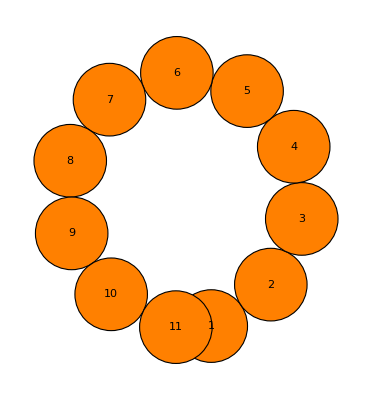

```mathematica
Graphics[chainGraphic[newPositions]]
```